```mathematica
z[c_,H_, u_,p_]:=2*(c^H)*(u*p^c+1)/(u*p+1)
```

```mathematica
lnz[c_,H_, u_,p_]:=Log[z[c,H,u,p]]
```

```mathematica
cu[H_,p_,u_]:=H*Exp[H+1]
```

```mathematica
p1 = Plot[{z[4,4,10^3,p],z[4,4,10^4,p],z[4,4,10^5,p],z[4,4,10^6,p]},{p,0,0.4},
PlotRange->{0,100},
Frame->{True},
PlotStyle -> Directive[Thickness[0.007]],
ScalingFunctions->{None,"Log"},
LabelStyle -> Directive[Black, FontSize->24]
]
```

-Graphics-

```mathematica
Show[p2,ImageSize->Large]
```

-Graphics-

```mathematica
p2 = ContourPlot[lnz[4,4,u,p],
{p, 0.001,0.4}, {u, 10^3, 10^6},
ScalingFunctions -> {None, "Log"},
PlotLegends -> Automatic,
LabelStyle -> Directive[Black, FontSize->24]
]
```

-Graphics-

```mathematica
Show[p2,ImageSize->Large]
```

-Graphics-

```mathematica
u=10^10 
ContourPlot[z[c,H,u,0.01],
{c, 4,12}, {H, 4,12}, 
 Contours -> {0.01,0.1,1,10,100},
PlotLegends -> Automatic,
LabelStyle -> Directive[Black, FontSize->24],
PlotLegends -> Automatic,
 ContourShading -> {
 RGBColor[38/255,84/255,138/255],
 RGBColor[76/255,104/255,164/255], 
 RGBColor[120/255,120/255,138/255], 
 RGBColor[164/255,135/255,113/255],
 RGBColor[208/255,150/255,87/255],
 RGBColor[233/255,167/255,85/255],
 RGBColor[240/255,184/255,107/255]}
]
```

10000000000

```mathematica
p=0.1;
H=4;
p3 = Plot[{z[c,H,10^3,p],z[c,H,10^4,p], z[c,H,10^5,p],z[c,H,10^6,p]},{c,1,8},
Frame->{True},
ScalingFunctions->{None,"Log"},
PlotRange->{-1,10},
PlotStyle -> Directive[Thickness[0.007]],
LabelStyle -> Directive[Black, FontSize->24],
GridLines->{{},{{1,Red}}}
]
```

-Graphics-

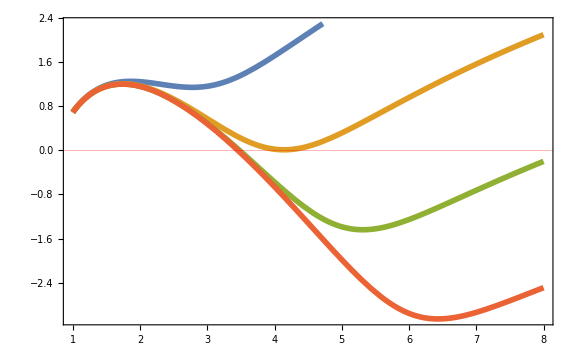

```mathematica
Show[p3,ImageSize->Large]
```

```mathematica
u=10^4;
p =0.1;
p4 = ContourPlot[lnz[c,H,u,p],
{c,2,7}, {H, 2,7},
PlotLegends -> Automatic,
LabelStyle -> Directive[Black, FontSize->24],
Contours->{-3,-2,-1,0,1,2,3}
]
```

-Graphics-

```mathematica
u = 1000;
p=0.1;
p5 = ContourPlot[lnz[c,H,u,p],
{c,2,8}, {H, 2,8},
PlotLegends -> Automatic,
LabelStyle -> Directive[Black, FontSize->24],
Contours->{-3,-2,-1,0,1,2,3}
]
```

-Graphics-

```mathematica
p6 = ContourPlot[lnz[6,6,u,p],
{p, 0,0.4}, {u, 1, 10^7},
ScalingFunctions -> {None, "Log"},
PlotLegends -> Automatic,
LabelStyle -> Directive[Black, FontSize->24]
]
```

-Graphics-

```mathematica
p7 = Plot[cu[3,p,u],{p,0,0.4},
PlotRange->{{0,0.4},{1,10^7}},
  ScalingFunctions -> {None, "Log"},
  PlotLegends -> Automatic,
  LabelStyle -> Directive[Black, FontSize->24],
  PlotStyle->{Directive[RGBColor[0,100/255,0],Thick]}
  ]
```

-Graphics-

```mathematica
Show[p6,p7]
```

-Graphics-